```mathematica
(* Morse Oscillator basis *)
```

```mathematica
s=SparseArray[{{i_,i_}->0,{i_,j_}/;i-j==-1->√(j-1)},{128,128}]
```

SparseArray[<127>, {128, 128}]

```mathematica
X:=N[s+Transpose[s]]
```

```mathematica
P:= ⅈ/2 N[(-s+Transpose[s])]
```

```mathematica
Reverse[N[Eigenvalues[P.P+MatrixPower[X,4]]]]
```

{1.06036,3.79967,7.4557,11.6447,16.2618,21.2384,26.5285,32.0986,37.923,43.9812,50.2563,56.7342,63.403,70.2529,77.2734,84.438,91.8009,99.4127,106.484,111.189,122.741,124.605,151.116,152.755,190.929,192.298,242.946,244.174,308.856,310.004,390.699,391.798,490.778,491.845,611.631,612.676,756.022,757.053,926.951,927.971,1127.65,1128.67,1361.62,1362.62,1632.59,1633.59,1944.6,1945.6,2301.96,2302.96,2709.32,2710.32,3171.63,3172.63,3694.23,3695.23,4282.83,4283.83,4943.56,4944.56,5683.01,5684.,6508.23,6509.22,7426.84,7427.83,8447.01,8448.,9577.57,9578.56,10828.,10829.,12208.7,12209.7,13730.7,13731.7,15406.3,15407.2,17248.4,17249.4,19271.6,19272.6,21491.6,21492.6,23925.6,23926.6,26592.7,26593.7,29514.,29515.,32712.9,32713.9,36215.5,36216.5,40051.3,40052.3,44253.5,44254.5,48859.8,48860.8,53913.7,53914.7,59465.5,59466.5,65574.2,65575.2,72309.6,72310.6,79756.,79757.,88016.4,88017.4,97220.2,97221.2,107533.,107534.,119178.,119179.,132461.,132462.,147841.,147842.,166058.,166059.,188511.,188512.,218727.,218728.}

```mathematica
Reverse[N[Eigenvalues[P.P+MatrixExp[2 X]-11.MatrixExp[ X]+25IdentityMatrix[128]]]]
```

{2.15087×10^-7,8.99998,15.9999,20.9996,21.6973,23.9998,25.0098,25.0873,25.2325,25.4407,25.7034,26.0252,26.3956,26.8253,27.2935,27.8081,28.1554,28.498,29.0803,29.736,30.438,31.1624,31.946,32.7524,33.6437,34.5497,35.5458,36.5159,37.5583,38.4875,39.5158,40.559,41.7563,43.0354,44.2379,45.4188,45.9253,47.5125,48.9113,50.6148,52.2077,54.0115,55.7625,57.6732,59.6064,61.5956,63.7242,65.6196,67.9829,69.3105,71.571,72.8156,75.5806,77.7337,-79.0063,80.9343,82.8875,87.1245,87.6392,93.2075,94.1546,101.032,101.431,107.946,110.269,114.009,126.079,140.257,155.705,-155.76,200.358,210.756,-249.751,286.019,398.424,693.791,774.709,1439.76,2675.66,4918.45,8961.39,16219.6,29218.4,52470.2,94049.3,168432.,301625.,540465.,969522.,1.74193×10^6,3.13584×10^6,5.65809×10^6,1.02355×10^7,1.85693×10^7,3.37939×10^7,6.17098×10^7,1.13097×10^8,2.08086×10^8,3.84457×10^8,7.13485×10^8,1.33041×10^9,2.49335×10^9,4.69815×10^9,8.90379×10^9,1.69785×10^10,3.25904×10^10,6.30016×10^10,1.22719×10^11,2.41006×10^11,4.77507×10^11,9.55181×10^11,1.93066×10^12,3.94686×10^12,8.16947×10^12,1.71427×10^13,3.65214×10^13,7.91335×10^13,1.74756×10^14,3.94345×10^14,9.12193×10^14,2.17186×10^15,5.35102×10^15,1.37421×10^16,3.71681×10^16,1.07549×10^17,3.41771×10^17,1.25492×10^18,6.08159×10^18}

```mathematica
Reverse[N[Eigenvalues[P.P+MatrixExp[2 X]-9.MatrixExp[ X]+25IdentityMatrix[128]]]]
```

{9.,16.,20.7486,21.,22.502,24.,25.0098,25.0863,25.2311,25.4373,25.6998,26.0169,26.3849,26.8036,27.2678,27.7756,28.3176,28.8887,29.4836,30.117,30.8057,31.5553,32.3637,33.2197,-33.792,34.1248,35.0656,36.054,37.0726,38.1483,39.2573,40.4375,41.6474,42.932,44.2273,45.5938,46.8866,48.0721,48.9574,50.3135,51.8164,53.4682,55.1797,57.0022,58.8613,60.8477,62.711,64.8277,66.0473,68.0558,69.2376,71.7594,73.8376,76.5304,78.9986,81.7054,82.6432,84.8743,88.4816,91.6866,95.1731,99.5478,100.376,-100.905,108.598,109.269,115.798,126.33,128.816,153.324,209.003,219.34,-239.669,259.4,384.573,462.556,833.651,1527.8,2790.7,5069.28,9160.18,16482.7,29568.,52935.5,94669.6,169259.,302730.,541944.,971501.,1.74458×10^6,3.13939×10^6,5.66286×10^6,1.02419×10^7,1.85779×10^7,3.38056×10^7,6.17255×10^7,1.13118×10^8,2.08115×10^8,3.84496×10^8,7.13539×10^8,1.33048×10^9,2.49345×10^9,4.69828×10^9,8.90398×10^9,1.69788×10^10,3.25908×10^10,6.30021×10^10,1.2272×10^11,2.41007×10^11,4.77508×10^11,9.55183×10^11,1.93067×10^12,3.94687×10^12,8.16947×10^12,1.71427×10^13,3.65214×10^13,7.91335×10^13,1.74756×10^14,3.94345×10^14,9.12193×10^14,2.17186×10^15,5.35102×10^15,1.37421×10^16,3.71681×10^16,1.07549×10^17,3.41771×10^17,1.25492×10^18,6.08159×10^18}

```mathematica
(* position space *)
```

```mathematica
Xp:=N[SparseArray[{i_,i_}->√((2π)/64)(2i-65)/2,{64,64}]]
```

```mathematica
matpos:=Table[1/(√64)Exp[(2π)/64 ⅈ((2j-65)(2k-65))/4],{j,1,64},{k,1,64}]
```

```mathematica
Pp:=Chop[N[(ConjugateTranspose[matpos].Xp).matpos]]
```

```mathematica
Reverse[N[Eigenvalues[Pp.Pp+MatrixExp[2 Xp]-11.MatrixExp[ Xp]+25IdentityMatrix[64]]]]
```

{-9.05732×10^-6,8.99979,15.9993,20.9992,23.9995,25.0541,25.4097,25.9963,26.7713,27.7157,28.8177,30.069,31.4636,32.9969,34.665,36.4649,38.3941,40.4507,42.6325,44.9381,47.3655,49.9122,52.575,55.3473,58.2227,61.1856,64.2321,67.3542,70.5936,73.9783,77.5716,81.3648,85.3935,89.6239,94.0999,98.7856,103.747,108.915,112.364,114.911,120.624,229.756,484.626,1003.27,2029.21,4024.22,7860.04,15178.3,29064.7,55313.1,104791.,197872.,372729.,700865.,1.31617×10^6,2.46935×10^6,4.62968×10^6,8.67562×10^6,1.62514×10^7,3.04342×10^7,5.69834×10^7,1.06677×10^8,1.99687×10^8,3.73762×10^8}

```mathematica
Xp1=N[SparseArray[{i_,i_}->√((2π)/64)(2i-65)/2,{64,64}]]
```

```mathematica
matpos1=Table[1/(√64)Exp[(2π)/64 ⅈ((2j-65)(2k-65))/4],{j,1,64},{k,1,64}]
```

```mathematica
Pp1=Chop[N[(ConjugateTranspose[matpos].Xp1).matpos1]]
```

```mathematica
Reverse[N[Eigenvalues[Pp1.Pp1+MatrixExp[2 Xp1]-11.MatrixExp[ Xp1]+25IdentityMatrix[64]]]]
```

$Aborted

```mathematica
Reverse[N[Eigenvalues[Pp.Pp+MatrixExp[2 Xp]-9.MatrixExp[ Xp]+25IdentityMatrix[64]]]]
```

{9.,16.,21.,24.,25.0512,25.391,25.9547,26.702,27.6147,28.6815,29.8948,31.249,32.7394,34.3627,36.1158,37.9964,40.0022,42.1315,44.3823,46.7538,49.2439,51.8528,54.5788,57.4235,60.3861,63.4705,66.676,70.006,73.4545,77.0071,80.6244,84.2065,87.6989,91.2529,95.2328,99.5969,104.372,109.429,114.956,120.688,139.805,268.762,538.243,1076.69,2129.67,4161.64,8048.03,15435.4,29416.5,55794.4,105450.,198773.,373961.,702550.,1.31848×10^6,2.4725×10^6,4.634×10^6,8.68152×10^6,1.62594×10^7,3.04452×10^7,5.69985×10^7,1.06698×10^8,1.99715×10^8,3.738×10^8}

```mathematica
(* finite diff method *) 

Xfd:=SparseArray[{i_,i_}->(2i-129)/2 ,{128,128}]

s=SparseArray[{{i_,i_}->1,{i_,j_}/;i-j==-1->-1},{128,128}]

P2:= s+Transpose[s]

Reverse[N[Eigenvalues[(8)(8)P2+ 1/((8)(8)(8)(8))MatrixPower[Xfd,4]]]]

Reverse[N[Eigenvalues[(8)(8)P2+ 1/((8)(8))MatrixPower[Xfd,2]]]]

Reverse[N[Eigenvalues[(8)(8)P2+MatrixExp[.25 Xfd]-11.MatrixExp[ .125 Xfd]+25IdentityMatrix[128]]]]

Reverse[N[Eigenvalues[(8)(8)P2+MatrixExp[.25 Xfd]-9.MatrixExp[ .125 Xfd]+25IdentityMatrix[128]]]]

Plot[{-ⅇ^-x+(5-ⅇ^-x)^2,ⅇ^-x+(5-ⅇ^-x)^2 ,ⅇ^-x+(4-ⅇ^-x)^2+9,ⅇ^-x+(3-ⅇ^-x)^2+9+7,ⅇ^-x+(2-ⅇ^-x)^2+9+7+5},{x,-3,5},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V(x)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]},PlotRange->{-6,35}]
```

```mathematica
h=1;V[x_]:=(5)^2+(Exp[-x])^2-(2(5)+1)Exp[-x]
ℒ=-h^2*u''[x]+V[x]*u[x];{vals,funs}=NDEigensystem[ℒ,u[x],{x,-10,10},5,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

```mathematica
vals
```

```mathematica
{3.945822613507399*^-9,9.000000016754132,16.000000033074905,21.00000003936596,23.99999977973254}

Show[Plot[Evaluate[h*funs+vals],{x,-5,5},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_M(x)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}],Plot[V[x],{x,-5,5},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_(x)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}],PlotRange->{{-5,5},{-5,25}},AxesOrigin->{-5,0},ImageSize->Medium]
```

```mathematica
h=1;V[x_]:=(5)^2+(Exp[-x])^2-(2(5)+1)Exp[-x]
ℒ=-h^2*u''[x]+V[x]*u[x];{vals,funs}=NDEigensystem[ℒ,u[x],{x,-10,10},5,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

```mathematica
vals
```

{3.94582×10^-9,9.,16.,21.,24.}

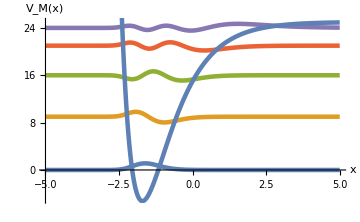

```mathematica
Show[Plot[Evaluate[h*funs+vals],{x,-5,5},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_M(x)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}],Plot[V[x],{x,-5,5},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_(x)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}],PlotRange->{{-5,5},{-5,25}},AxesOrigin->{-5,0},ImageSize->Medium]
```